# Calculating Scintillator Compton Spectra

Contents

Compton Scattering Formulas

Detector Resolution

Package Initialization and Definitions

User Notes

Compton Scattering Formulas

Calculation of the probability of the scattering of a single high-energy photon by a single free electron initially at rest requires a fairly sophisticated quantum theory called Quantum Electrodynamics. The resulting equation is known as the Klein-Nishina formula, first derived jointly by Oskar Klein and Yoshio Nishina in 1929. The differential cross section for such scattering (integrated over all polarization states of the photon and electron) is given by the simple formula:

ⅆσ/ⅆΩ=r_e^2/2(k/k_0)^2(k/k_0+k_0/k-sin^2 θ)

Where θ is the angle from the inital photon path to the scattered photon path,  ⅆΩ=sin θ  ⅆθ ⅆϕ is the differential solid angle about the angles θ and ϕ (defining the outgoing photon direction), k_0=ℏω_0 is the initial photon energy, k is the outgoing photon energy, r_e is the classical electron radius, and σ is the scattering cross section. Even though expression (DisplayFormulaNumbered) is simple, its derivation is subtle and is beyond the scope of this text.

The length r_e is one of the natural units of length for the electrodynamics of the electron and is formed from the electron’s rest energy and charge. In Gaussian units, it is given by:

r_e=e^2/m_e=2.817×10^-13 cm

It is called the classical electron radius because a thin spherical shell of total charge e and radius r_e would have a total Coulomb potential energy of m_e=0.511 MeV, the rest energy of the electron. The situation for an actual electron is much more complex — this classical calculation doesn't include Planck’s constant ℏ, and, as you might therefore expect, r_e is not relevant to a full quantum mechanical description of the electron. Interestingly, however, r_e turns out to be of the same order as the radius of a typical atom’s nucleus.

The outgoing photon energy k can be derived from the incoming photon energy k_0 and the electron rest energy m_e using simple relativistic kinematics of an elastic collision of two point particles (that is, using conservation of energy and linear momentum), where the photon’s rest mass is 0:

k_0/k=1+k_0/m_e(1-cos θ)

The recoil kinetic energy of the target electron is simply the difference t_e=k_0-k. The maximum recoil kinetic energy the electron could receive happens when θ=π; in this case we have:

k_min=(1/k_0+2/m_e)^-1
(t_e)_max=k_0-k_min

The minimum outgoing photon energy k_min is called the backscatter energy and approaches m_e/2 for large k_0. The maximum electron recoil kinetic energy defines the Compton edge, the maximum energy observed in a scintillator Compton scattering spectrum. The minimum electron recoil kinetic energy is, of course, 0 (when θ=0) The functions BackscatterEdge[] and ComptonEdge[] are provided to calculate k_min and (t_e)_max.

To calculate the expected Compton scattering spectrum observed in a scintillation detector, we need to know the probability of scattering as a function of the electron's recoil kinetic energy, since it is this energy to which the detector responds. To convert equation (DisplayFormulaNumbered) to an expression for ⅆσ/ⅆ t_e, we note that:

ⅆσ/(ⅆ t_e)=ⅆσ/ⅆΩ ⅆΩ/(ⅆ t_e)=ⅆσ/ⅆΩ ⅆΩ/ⅆθ ⅆθ/(ⅆ t_e)=-ⅆσ/ⅆΩ ⅆΩ/ⅆθ ⅆθ/ⅆk

Now, since we want Ω (θ) in this expression, we must integrate over the azimuth angle ϕ, so that   ⅆΩ(θ)=2π sin θ  ⅆθ, and from equation (DisplayFormulaNumbered):

ⅆθ/ⅆk=ⅆ/ⅆk(k_0/k)/ⅆ/ⅆθ(k_0/k)=-(k_0/k^2)/(k_0/m_e sin θ)=-m_e/(k^2 sin θ)
∴ⅆσ/(ⅆ t_e)=(2π m_e)/k^2 ⅆσ/ⅆΩ

From equation (DisplayFormulaNumbered), we can get an expression for θ to substitute into (DisplayFormulaNumbered) and then (DisplayFormulaNumbered):

cos θ=1-(m_e(k_0-k))/(k_0 k)=1-(m_e t_e)/(k_0 k)
∴sin^2 θ=2((m_e t_e)/(k_0 k))-((m_e t_e)/(k_0 k))^2

∴ⅆσ/(ⅆ t_e)=((π m_e r_e^2)/k_0^2)(k/k_0+k_0/k-2((m_e t_e)/(k_0 k))+((m_e t_e)/(k_0 k))^2) ; k=k_0-t_e

To convert the expression (DisplayFormulaNumbered) into a probability density for observing Compton scattered electrons with various recoil energies t_e, we note that the probability density is proportional to the differential cross section ⅆσ/ⅆ t_e, but must be normalized so that the total probability is 1:

P(t_e ;k_0)ⅆ t_e∝(k/k_0+k_0/k-2((m_e t_e)/(k_0 k))+((m_e t_e)/(k_0 k))^2) ⅆ t_e 
∫_0^((t_e)_max) P(t_e ;k_0)ⅆ t_e=1

∴P_Compton(t_e ;k_0)=1/A(k/k_0+k_0/k-2((m_e t_e)/(k_0 k))+((m_e t_e)/(k_0 k))^2) ; k=k_0-t_e
A≡(2(k_0^3+9 k_0^2 m_e+8 k_0 m_e^2+2 m_e^3))/(2 k_0+m_e)^2+(2 k_0-4 m_e-(4 m_e^2)/k_0)tanh^-1(k_0/(k_0+m_e))

The following figure shows a plot of P(t_e) from equation (DisplayFormulaNumbered) for an incoming photon with k_0=0.662 MeV (this plot was generated using the function ComptonPDF[]):

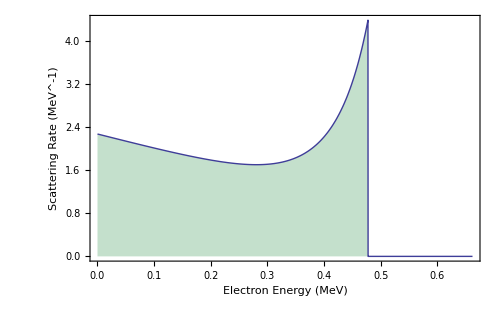

back to contents

Detector Resolution

Following a Compton scattering event in a scintillation detector the outgoing electron loses most of its kinetic energy by ionizing other atoms in the scintillator material. Eventually most of the original energy deposited by the incoming photon is converted to the total ionization energy of many slowly-moving electrons in the material (the electrons are near the bottom of the conduction band of the scintillator material). The scintillator material is engineered so that these electrons recombine with the ionized atoms mainly through the efficient production of visible-light photons. Many of these photons are detected by a photomultiplier tube attached to the scintillator, and it is the photomultiplier’s output signal which is amplified and analyzed to estimate the energy deposited in the scintillator material by the incoming photon.

Unfortunately, only a fraction of the visible-light photons generated by the scintillator are absorbed by the photomultiplier’s photocathode (this fraction defines the quantum efficiency of the detector). Nearly all of the absorbed photons cause a photoelectron to be emitted by the photocathode. The collection of photoelectrons comprise the signal which is then amplified by the photomultiplier to produce its output. The absorption of any particular photon is random; the statistics of the absorption process are well-described by the Poisson distribution, a discrete distribution with the single parameter μ, the expected (mean) number of events. Equations (DisplayFormulaNumbered) and (DisplayFormulaNumbered) give the probability density functions of the Poisson and the familiar normal (Gaussian) distributions:

Poisson Distribution:   P_P(k ;μ)=(ⅇ^-μ μ^k)/(k!)

Normal Distribution:   P_G(x ;μ,σ^2)=1/(√(2π σ^2))ⅇ^(-(x-μ)^2/(2 σ^2))

The variance of the Poisson distribution is equal to its mean, μ. For μ≫1, the Poisson distribution approaches that of a normal distribution with mean and variance both equal to μ, as illustrated by the following figure:

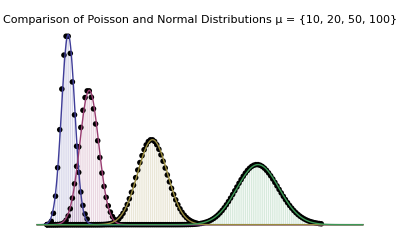

Since the standard deviation grows only as √μ, the family of Poisson distributions is characterized by peaks which are relatively more well-defined for larger μ values.

A well-engineered scintillation detector produces a number of visible-light photons which is very nearly proportional to the energy deposited by an incoming high-energy photon over a wide range of energies. The quantum efficiency of the system is also nearly independent of the number of visible-light photons produced, so that a scintillation system’s resolution as a function of energy may be accurately characterized by a single parameter: the average energy per photoelectron, or e_pe. The kinetic energy a high-energy photon imparts to a scintillator electron during a Compton scatter, t_e, will on average result in the generation of μ=t_e/e_pe photoelectrons by the photomultiplier’s photocathode. The actual number of photoelectrons produced by events with energy t_e will vary randomly, as samples of the Poisson distribution with mean t_e/e_pe. This distribution has a fractional standard deviation of √μ/μ=√(e_pe/t_e), so the resolution of the scintillation detector improves as e_pe is made smaller. Typical values for e_pe range from ≲1000 eV for a good sodium iodide (NaI) scintillator to  >5000 eV for a plastic (organic) scintillator.

The finite resolution of the detector can be modeled by its response function, R(t ;t_e,e_pe). The response function is a distribution which gives the probability density that the detector will respond with an output corresponding to energy t as a result of energy t_e actually being deposited in the scintillator. Since the detector output is characterized by the discrete Poisson distribution, the response function R(t ;t_e,e_pe) must be discrete as well. We will, however, make use of the similarity of the normal and Poisson distributions for large μ and consider  R(t ;t_e,e_pe) to be well represented by the continuous normal distribution, equation (DisplayFormulaNumbered), with mean and variance determined by the values of t_e and e_pe, as shown in equation (DisplayFormulaNumbered).

R(t ;t_e,e_pe)=P_G(t ;t_e,e_pe t_e)=1/(√(2π e_pe t_e))ⅇ^(-(t-t_e)^2/(2 e_pe t_e))

With the response function R in hand, the observed Compton spectrum of an incoming photon with energy k_0, which includes the effects of the finite detector resolution, may be calculated. The expression for the probability density of the measured energy t involves a generalization of a convolution integral of the Compton scattering distribution (DisplayFormulaNumbered) and the response function (DisplayFormulaNumbered), as shown in expression (DisplayFormulaNumbered).

P_observed(t ;k_0,e_pe)=∫_0^((t_e)_max) R(t ;t_e,e_pe)P_Compton(t_e ;k_0)ⅆ t_e

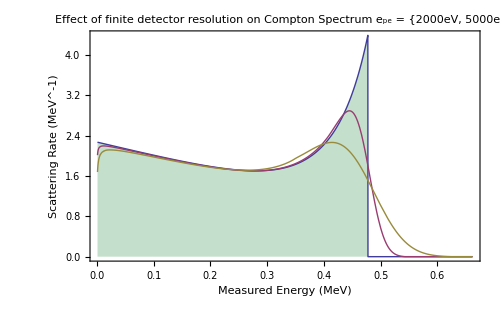

The figure above shows the results of the convolution on the measured Compton scattering distribution for an incoming photon with k_0=0.662MeV. This figure was generated using the functions ComptonPDF[] and SmoothedComptonPDF[].

back to contents

Package Initialization and Definitions

This section contains the initialization code and the definitions of the functions and variables in this Compton package.

### Initialization: Check the Mathematica version and start the application

```mathematica
If[!TrueQ[$VersionNumber≥ 6.0],
NotebookPut[Notebook[{Cell["You need Mathematica v. 6 or higher to run this application.","Subsubtitle" ],ButtonBox["\tOK\t",ButtonFrame->"DialogBox",Active->True,ButtonFunction:>(NotebookClose[ButtonNotebook[]]&),ButtonMargins-> 5]
},
ShowCellBracket->False,Saveable->False,
WindowTitle->"Compton",
WindowElements-> {},
WindowFloating-> True,
WindowFrame-> "ModalDialog",
WindowSize->{250,100}
]
];NotebookClose[EvaluationNotebook[]],
NotebookLocate["package"];
SelectionMove[EvaluationNotebook[],All,CellGroup];
SelectionEvaluateCreateCell[EvaluationNotebook[]];
SelectionMove[EvaluationNotebook[],Before,Notebook]
];
```

## package definitions

### The public symbols defined by the package

```mathematica
If[!TrueQ[$VersionNumber≥ 7.0],
BeginPackage["Compton`",{"NonlinearRegression`"}];
$ContextPath=Join[{"NonlinearRegression`","RegressionCommon`"},$ContextPath],
BeginPackage["Compton`"]
];

(* clear everything first, so the definitions may be read multiple times *)
Unprotect["`*"]; 
ClearAll["`*"];
```

```mathematica
comptonPalette::usage="Starts the Compton Spectrum palette.";

ComptonEdge::usage="ComptonEdge[k_0,m_e] gives the Compton edge energy for incoming photon energy k_0 and electron rest energy m_e. ComptonEdge[k_0] assumes k_0 in MeV and m_e = 0.511 MeV.";

BackscatterEdge::usage="BackscatterEdge[k_0,m_e] gives the minimum Compton outgoing photon energy for incoming photon energy k_0 and electron rest energy m_e. BackscatterEdge[k_0] assumes k_0 in MeV and m_e = 0.511 MeV.";

ComptonPDF::usage="ComptonPDF[t_e,k_0,m_e] gives the probability density distribution for outgoing electron kinetic energy t_e, given incoming photon energy k_0 and electron rest energy m_e. ComptonPDF[t_e,k_0] calculates the probability density assuming t_e and k_0 are given in MeV, and m_e = 0.511 MeV.";

Co60PDF::usage="Co60PDF[t_e,ρ,m_e] gives the probability density distribution for outgoing electron kinetic energy t_e, given an incoming Cobalt-60 photon with energy of 1.173MeV or 1.332MeV and electron rest energy m_e. The argument ρ gives the relative scintillator detection rate for 1.173MeV photons to 1.332MeV photons. It is typically very nearly equal to 1. Co60PDF[t_e,ρ] calculates the probability density assuming t_e is given in MeV, and m_e = 0.511 MeV. Co60PDF[t_e] further assumes ρ = 1.";

ScintillatorResponse::usage="ScintillatorResponse[t,t_e,e_pe] gives the probability density distribution for observing an outgoing Compton electron with actual kinetic energy t_e (in MeV) at the observed energy t (in MeV), given a scintillator-photomultiplier responsivity of e_pe average energy deposited per photoelectron (in eV).";

SmoothedComptonPDF::usage="SmoothedComptonPDF[t,k_0,e_pe] numerically calculates the probability density distribution for a scintillator detected energy t (in MeV), given incoming photon energy k_0 (in MeV) and a scintillator-photomultiplier responsivity of e_pe average energy deposited per photoelectron (in eV). It does a numerical calculation of the convolution integral of ComptonPDF[t_e,k_0] and ScintillatorResponse[t,t_e,e_pe].";

SmoothedCo60PDF::usage="SmoothedComptonPDF[t,e_pe,ρ] numerically calculates the probability density distribution for a scintillator detected energy t (in MeV), given incoming Cobalt-60 photons with energies of 1.173MeV and 1.332MeV, a scintillator-photomultiplier responsivity of e_pe average energy deposited per photoelectron (in eV), and ρ = (probability of detection of a 1.173MeV photon)/(probability of detection of a 1.332MeV photon), which should be very nearly equal to 1. It does a numerical calculation of the convolution integral of ComptonPDF[t_e,k_0] and ScintillatorResponse[t,t_e,e_pe].";

NonlinFit::usage="NonlinFit[parameters] performs a nonlinear regression by calling the appropriate Mathematica routine, based on the Mathematica version (6.x or 7.x). It is called by ComptonFit[ ] and Co60Fit[ ].";

ComptonFit::usage="ComptonFit[k_0,e_pe,x_edge] performs a CurveFit-compatible fit of a measured scintillator spectrum to a single-photon Compton scattering distribution. When calling ComptonFit[ ] k_0, e_pe, and x_edge must all be given numerical values: k_0 is the incoming photon energy (in MeV), e_pe is an initial estimate of the average energy deposited per photoelectron (in eV), and x_edge is an initial estimate of the X position of the Compton edge (channel number).";

fCompton::usage="fCompton[x] gives the expected y(x) resulting from calling ComptonFit[ ] on a measured scintillator spectrum. This function is also called by CurveFit's fY[x] following a call to ComptonFit[ ].";

ComptonFitParameters::usage="a list of the symbol names of the fit parameters set by calling ComptonFit[ ].";
ComptonFitParameters = SymbolName/@{EPE,K0,sigEPE,sigXedge,sigXscale,sigYoffset,sigYscale,Tedge,Xedge,Xscale,Yoffset,Yscale};

(MessageName[#,"usage"]=SymbolName[#]<>" is a fit parameter set by calling ComptonFit[ ].")&/@Symbol/@ComptonFitParameters;

Co60Fit::usage="Co60Fit[e_pe,x_edge] performs a CurveFit-compatible fit of a measured Co60 scintillator spectrum to a sum of Compton scattering distributions due to the two Cobalt-60 gamma photons. When calling Co60Fit[ ] e_pe and x_edge must be given numerical values: e_pe is an initial estimate of the average energy deposited per photoelectron (in eV) and x_edge is an initial estimate of the X position of the 1.33 MeV photon Compton edge (channel number).\n\n"<>
"Co60Fit[ ] chooses e_pe and x_edge by using the fit results of a previous call to ComptonFit[ ].";

fCo60::usage="fCo60[x] gives the expected y(x) resulting from calling Co60Fit[ ] on a measured scintillator spectrum. This function is also called by CurveFit's fY[x] following a call to Co60Fit[ ].";

Co60Ratio::usage = "Co60Ratio is a fit parameter set by calling Co60Fit[ ]. It gives the ratio of 1.173MeV:1.332MeV detections in the observed scintillator spectrum and should be approximately equal to 1.";

Compton`sigCo60Ratio::usage = "sigCo60Ratio is a fit parameter set by calling Co60Fit[ ]. It gives the estimated uncertainty in the determination of Co60Ratio.";
```

```mathematica
Begin["`Private`"];

(* clear everything first, so the definitions may be read multiple times *)
Unprotect["`*"]; 
ClearAll["`*"];
```

### Managing dialog windows

```mathematica
EdgeBackOpen=False;
singleComptonSpectrumOpen=False;
Co60ComptonSpectrumOpen=False;
comptonPaletteOpen=False;
If[TrueQ[Head[EdgeBackNotebook]===NotebookObject],NotebookClose[EdgeBackNotebook]];
If[TrueQ[Head[singleComptonSpectrumNotebook]===NotebookObject],NotebookClose[singleComptonSpectrumNotebook]];
If[TrueQ[Head[Co60ComptonSpectrumNotebook]===NotebookObject],NotebookClose[Co60ComptonSpectrumNotebook]];
If[TrueQ[Head[comptonPaletteNotebook]===NotebookObject],NotebookClose[comptonPaletteNotebook]];
If[TrueQ[Head[comptonAskDialog]===NotebookObject],NotebookClose[comptonAskDialog]];
EdgeBackNotebook = Notebook[{}];
singleComptonSpectrumNotebook = Notebook[{}];
Co60ComptonSpectrumNotebook = Notebook[{}];
ComptonFitNotebook = Notebook[{}];
Co60FitNotebook= Notebook[{}];
comptonPaletteNotebook = Notebook[{}];
helpNotebook = Notebook[{}];
comptonAskDialog=Notebook[{}];
```

### Compton scattering functions

#### Compton edge energy

```mathematica
tMax[k0_,me_:0.5109989]:=
(2 k0)/(2+me/k0)

ComptonEdge[k0_,me_:0.5109989]:=tMax[k0,me]
BackscatterEdge[k0_,me_:0.5109989]:=k0-tMax[k0,me]
```

#### Compton scattering probability density function

```mathematica
dRaw[te_,k0_,me_:0.5109989]:=
Block[{k=k0-te, r1, r2},
r1 = k/k0;
r2 = me te/(k k0);
r1+1/r1+r2(r2-2)
]

dFull[te_,k0_,me_:0.5109989]:=If[te>tMax[k0,me],
0,
Evaluate[dRaw[te,k0,me]]
]

dNorm[k0_,me_:0.5109989]:=(2 (k0^3+9 k0^2 me+8 k0 me^2+2 me^3))/(2 k0+me)^2+(2 k0-4 me-(4 me^2)/k0) ArcTanh[k0/(k0+me)]

ComptonPDF[te_,k0_,me_:0.5109989]:=dFull[te,k0,me]/dNorm[k0,me]

Co60PDF[te_,ratio_:1,me_:0.5109989]:=(ratio ComptonPDF[te,1.173,me]+ComptonPDF[te,1.332,me])/(1+ratio)
```

### Scintillator resolution and convolution with Compton spectrum

#### Scintillator response function (resolution)

```mathematica
response[
t_ (* observed energy MeV *),
te_ (* actual energy MeV *),
epe_(* energy/photoelectron eV *)
]:=
PDF[NormalDistribution[te,Sqrt[te epe/10^6]],t]

ScintillatorResponse[t_,te_,epe_]:=response[t,te,epe]
```

#### Convolution of Compton PDF with scintillator response

```mathematica
dSmooth[
t_ (* observed energy MeV *),
k0_ (* photon energy MeV *),
epe_(* energy/photoelectron eV *),
sigmas_:3(* number of sigmas around peak to use *)
]:=
Block[{low, high, sig,max,x},
(* Calculate limits of convolution*)
max = tMax[k0];
sig =Sqrt[Min[t,max] epe/10^6];
high = Min[max,t+sigmas sig];
low = Max[0,t-sigmas sig];
(* Perform the convolution *)
If[t < 0||low>=high||t> sigmas max,
 0,
Quiet[NIntegrate[
dRaw[x,k0]response[t,x,epe],{x,low,high},Method->{"GlobalAdaptive",Method->{"TrapezoidalRule","Points"->10,"RombergQuadrature"->True},"SingularityDepth"->∞},
PrecisionGoal->3,AccuracyGoal->3
]]
]
]
```

```mathematica
SmoothedComptonPDF[
t_ (* observed energy MeV *),
k0_ (* photon energy MeV *),
epe_(* energy/photoelectron eV *),
sigmas_:3(* number of sigmas around peak to use *)
]:=dSmooth[t,k0,epe,sigmas]/dNorm[k0]
```

```mathematica
SmoothedCo60PDF[
t_ (* observed energy MeV *),
epe_(* energy/photoelectron eV *),
ratio_:1.044(* ratio of 1.173:1.332 gamma probability of detection *),
sigmas_:3(* number of sigmas around peak to use *)
]:=(ratio SmoothedComptonPDF[t,1.173,epe,sigmas]+SmoothedComptonPDF[t,1.332,epe,sigmas])/(1+ratio)
```

```mathematica
dSmoothInterp[k0_?NumberQ,epe_?NumberQ,sigmas_:3]:=
Block[{points,edge=tMax[k0],w=Sqrt[tMax[k0] epe/10^6],p1,p2},
p1=Max[.01,edge-5w];
p2=Max[.01,edge-30w];
points=Union[
{{.01,dSmooth[.01,k0,epe,sigmas]}},
Table[{t,dSmooth[t,k0,epe,sigmas]},{t,p1,edge+5w,w/3}],
If[p1-w/2>.01,
Table[{t,dSmooth[t,k0,epe,sigmas]},{t,p2,p1-w/2,1.5w}],
{}
],
If[p2-w>.01,
Table[{t,dSmooth[t,k0,epe,sigmas]},{t,.01,p2-w,edge/20}],
{}
],
Table[{t,dSmooth[t,k0,epe,sigmas]},{t,Min[k0,edge+5.5w],Max[1.3 k0,edge+5.5w],k0/20}]
];
psave=points;
Interpolation[points,InterpolationOrder->3]
]
```

### Single-gamma Compton fitting functions

#### Nonlinear Regression function (depends on Mathematica version)

```mathematica
If[TrueQ[$VersionNumber≥ 7.0],
(* Version 7 nonlinear fits *)
NonlinFit[p__]:=Block[{model},
model=NonlinearModelFit[p];
{model["EstimatedVariance"],
model["BestFitParameters"],
model["ParameterErrors"]/Sqrt@model["EstimatedVariance"]}
],
(* Version 6 nonlinear fits *)
NonlinFit[p__]:=Block[{model},
model=NonlinearRegress[p,RegressionReport->{BestFitParameters,AsymptoticCovarianceMatrix,EstimatedVariance}];
{(EstimatedVariance/.model),(BestFitParameters/.model),Sqrt@(Diagonal@First@(AsymptoticCovarianceMatrix/.model)/(EstimatedVariance/.model))}
]
];
```

#### data subset selection parameters

```mathematica
Clear[threshold,fraction,points]
threshold=0.;fraction=1./3.5;points=50;
```

#### data used to find fit parameter initial values

```mathematica
Clear[dataX,dataY,dataSY,data,offset, xscale, yscale,epe]
dataX=dataY=dataSY=data={};
```

#### Find the upper edge index of relevant data to fit, based on a value threshold

```mathematica
FindEdge[d_List,y_]:= First[Last[Position[d,x_/;x≥y]]]
```

#### Select a data subset to identify the Compton spectrum

```mathematica
indexRange[yData_List]:=
Block[{yvals=Select[yData,#>2&],min,yedge,iLo,iHi,iEdge},
Clear[offset];
offset=min=Ceiling[Min[yvals]+Sqrt[Min[yvals]]];
yedge=threshold(Mean[yvals]-min)+min;
iHi=FindEdge[yData,yedge];
iLo=Floor[fraction iHi];
{iLo,iHi}
]

dataSelect[xData_List,yData_List,syData_List]:=
Block[{iLo,iHi,len,r},
{iLo,iHi}=indexRange[yData];
Clear[dataX,dataY,dataSY];
{dataX,dataY,dataSY}=
{xData[[iLo;;iHi]],yData[[iLo;;iHi]],syData[[iLo;;iHi]]};
len=Length[dataX];
r=Floor[len/points];
If[r<2,data=Transpose[{dataX,dataY}];Return[]];
dataY=MovingAverage[dataY,r][[1;;len-r;;r]];
dataSY=Sqrt[MovingAverage[dataSY^2,r]][[1;;len-r;;r]];
dataX=dataX[[1+Floor[r/2];;len;;r]];
dataX=Take[dataX,Length[dataY]];
data=Transpose[{dataX,dataY}];
]
```

#### Estimate position of Compton edge and X and Y scale factors

```mathematica
initialScale[k0_,EPE_:3000]:=
Block[{p=dSmooth[tMax[k0],k0,EPE,3]/dNorm[k0],x,y},
{x,y}=data[[ FindEdge[dataY,.5(Median[dataY]+Mean[dataY])-offset] ]];
Clear[xscale,yscale,epe];
epe=EPE;
xscale=x/tMax[k0];
yscale=(y-offset)/p;
]

refineScale[k0_]:=
Block[{f1,f2,xs,ys,off,x,n},
f1=dSmoothInterp[k0,epe,5];
n=dNorm[k0];
f2[xs_,ys_,off_]:=(f1[#/xs]ys/n+off)&;
{xscale,yscale,offset}={xs,ys,off}/.Quiet[FindFit[data,f2[xs,ys,off][x],{{xs,xscale},{ys,yscale},{off,offset}},x]];
]
```

#### Refine epe estimate

```mathematica
refineEpe[k0_]:=
Block[{g,x,ep,norm=dNorm[k0],tempcell},
g[x_?NumberQ,ep_?NumberQ]:=dSmooth[x/xscale,k0,ep,3]yscale/norm+offset;
tempcell=PrintTemporary["Working... epe = "<>ToString[epe]];
epe=ep/.Quiet[FindFit[data,g[x,ep],{{ep,epe}},x,
StepMonitor:>(NotebookDelete[tempcell];tempcell=PrintTemporary["Working... epe = "<>ToString[ep]]),
PrecisionGoal->3,AccuracyGoal->3]]
]
```

#### Refine estimates of all parameters

```mathematica
refineAll[k0_]:=
Block[{g,x,ep,xs,ys,off,norm=dNorm[k0],tempcell},
g[x_Real,ep_Real,xs_Real,ys_Real,off_Real]:=dSmooth[x/xs,k0,ep,3]ys/norm+off;
tempcell=PrintTemporary["Working... epe = "<>ToString[epe]];
{xscale,yscale,offset,epe}=
{xs,ys,off,ep}/.Quiet[FindFit[data,g[x,ep,xs,ys,off],{{ep,epe},{xs,xscale},{ys,yscale},{off,offset}},x,
StepMonitor:>(NotebookDelete[tempcell];tempcell=PrintTemporary["Working... epe = "<>ToString[ep]]),
PrecisionGoal->3,AccuracyGoal->3]]
]
```

#### ComptonFit - CurveFit compatible fitting

```mathematica
Compton`ComptonFit[k0_?NumberQ,ep0_?NumberQ,edge0_?NumberQ,opts:OptionsPattern[]]:=
Block[{norm=dNorm[k0],t0=tMax[k0],xs0,i0,ys0,off0,f,g,step=0,data,wts,x,xs,ys,of,ep,results},

If[!CurveFit`CheckLength[], Abort[]];
data=Transpose[{CurveFit`xx,CurveFit`yy}];

(* the function to fit *)
f[x_?NumberQ,ep_?NumberQ,xs_?NumberQ,ys_?NumberQ,of_?NumberQ]:=(dSmooth[x/xs,k0,ep]/norm)ys+of;

CurveFit`Private`funct="y(x) = Compton spectrum from a photon with energy \!\(\*SubscriptBox[\(k\), \(0\)]\), scaled in X and Y and convolved with the scintillator resolution \!\(\*SubscriptBox[\(e\), \(pe\)]\)(energy/photoelectron).\n";

Print["n = ",CurveFit`n];
Print[CurveFit`Private`funct];

(* initialize scale factors and y offset *)
xs0=edge0/t0;
i0=First@Flatten@Position[CurveFit`xx,x_/;x≥edge0];
off0=Last[CurveFit`yy];
ys0=(CurveFit`yy[[ i0 ]]-off0)/(dSmooth[t0,k0,ep0]/norm);

(* unweighted fit *)
Print["Fit of (x,y)  (unweighted)"];
step=0;
results=Monitor[NonlinFit[data,
f[x,ep,xs,ys,of],
{{ep,ep0},{xs,xs0},{ys,ys0},{of,off0}},x,
EvaluationMonitor:>(step++),PrecisionGoal->3,AccuracyGoal->3,MaxIterations->20],
If[step<2,
Style["Initializing. This could take a while...","Subsubsection"],
Row[{Style["Minimizing χ^2.","Subsubsection"],ProgressIndicator[step/100.,Indeterminate]},"  "]]
];
If[!NumberQ[First[results]],Print["Solution not found!"];Abort[]];

(* set resulting values *)
Clear[Compton`K0,Compton`Tedge,Compton`EPE,Compton`Xedge,Compton`Xscale,Compton`Yscale,Compton`Yoffset,Compton`sigEPE,Compton`sigXedge,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset,Compton`fCompton];

Compton`K0=k0;Compton`Tedge=t0;
{Compton`EPE,Compton`Xscale,Compton`Yscale,Compton`Yoffset}=({ep,xs,ys,of}/.results[[2]]);
{Compton`sigEPE,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset}=results[[3]];
Compton`Xedge = Compton`Tedge Compton`Xscale;
Compton`sigXedge = Compton`Tedge Compton`sigXscale;

g=dSmoothInterp[Compton`K0,Compton`EPE];
Compton`fCompton[x_]:=Evaluate[(g[x/Compton`Xscale]/norm)Compton`Yscale+Compton`Yoffset];
CurveFit`Private`yff[x_]:=Compton`fCompton[x];
CurveFit`fY=Function[{x},Compton`fCompton[x]];
CurveFit`Private`ssy=0. CurveFit`yy+First[results];

CurveFit`Private`results=TableForm[{
{{"K0 (MeV) = ",Compton`K0},{"Tedge (MeV) = ",Compton`Tedge}},
{{"EPE (eV/photoelectron) = ",Compton`EPE},{"sigEPE = ",Compton`sigEPE}},
{{"Xscale (channels/MeV) = ",Compton`Xscale},{"sigXscale = ",Compton`sigXscale}},
{{"Yscale = ","(counts/channel)/(probability/MeV)",Compton`Yscale},{"sigYscale = ",Compton`sigYscale}},
{{"Yoffset (counts/channel) = ",Compton`Yoffset},{"sigYoffset = ",Compton`sigYoffset}},{{"Xedge (channel) = ",Compton`Xedge},{"sigXedge = ",Compton`sigXedge},{"Std. deviation = ",First[results]}}
}];

Print[CurveFit`Private`results];

(* weighted fit with sy *)
If[Min[CurveFit`sy]≤0.,Return[]];
Print["Fit of (x,y±\!\(σ\_y\))  "];
wts=1/CurveFit`sy^2; 
step=0;
results=Monitor[NonlinFit[data,
f[x,ep,xs,ys,of],
{{ep,Compton`EPE},{xs,Compton`Xscale},{ys,Compton`Yscale},{of,Compton`Yoffset}},x,
EvaluationMonitor:>(step++),PrecisionGoal->3,AccuracyGoal->3,MaxIterations->20,Weights->wts],
If[step<2,
Style["Initializing. This could take a while...","Subsubsection"],
Row[{Style["Minimizing χ^2.","Subsubsection"],ProgressIndicator[step/100.,Indeterminate]},"  "]]
];
If[!NumberQ[First[results]],Print["Solution not found!"];Abort[]];

(* set resulting values *)
Clear[Compton`K0,Compton`Tedge,Compton`EPE,Compton`Xedge,Compton`Xscale,Compton`Yscale,Compton`Yoffset,Compton`sigEPE,Compton`sigXedge,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset,Compton`fCompton];

Compton`K0=k0;Compton`Tedge=t0;
{Compton`EPE,Compton`Xscale,Compton`Yscale,Compton`Yoffset}=({ep,xs,ys,of}/.results[[2]]);
{Compton`sigEPE,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset}=results[[3]];
Compton`Xedge = Compton`Tedge Compton`Xscale;
Compton`sigXedge = Compton`Tedge Compton`sigXscale;

g=dSmoothInterp[Compton`K0,Compton`EPE];
Compton`fCompton[x_]:=Evaluate[(g[x/Compton`Xscale]/norm)Compton`Yscale+Compton`Yoffset];
CurveFit`Private`yff[x_]:=Compton`fCompton[x];
CurveFit`fY=Function[{x},Compton`fCompton[x]];
CurveFit`Private`ssy=CurveFit`sy;

CurveFit`Private`results=TableForm[{
{{"K0 (MeV) = ",Compton`K0},{"Tedge (MeV) = ",Compton`Tedge}},
{{"EPE (eV/photoelectron) = ",Compton`EPE},{"sigEPE = ",Compton`sigEPE}},
{{"Xscale (channels/MeV) = ",Compton`Xscale},{"sigXscale = ",Compton`sigXscale}},
{{"Yscale = ","(counts/channel)/(probability/MeV)",Compton`Yscale},{"sigYscale = ",Compton`sigYscale}},
{{"Yoffset (counts/channel) = ",Compton`Yoffset},{"sigYoffset = ",Compton`sigYoffset}},{{"Xedge (channel) = ",Compton`Xedge},{"sigXedge = ",Compton`sigXedge},{"\!\(\*SuperscriptBox[\(\[Chi]\), \(2\)]\) = ",First[results]}}
}];

Print[CurveFit`Private`results];

(* weighted fit with sx and sy *)
If[Min[CurveFit`sx]≤0.,Return[]];
Print["Fit of (x±\!\(σ\_x\),y±\!\(σ\_y\)) "];
wts=1/(CurveFit`sy^2+(fCompton'[CurveFit`xx]CurveFit`sx)^2); 
step=0;
results=Monitor[NonlinFit[data,
f[x,ep,xs,ys,of],
{{ep,Compton`EPE},{xs,Compton`Xscale},{ys,Compton`Yscale},{of,Compton`Yoffset}},x,
EvaluationMonitor:>(step++),PrecisionGoal->3,AccuracyGoal->3,MaxIterations->20,Weights->wts],
If[step<2,
Style["Initializing. This could take a while...","Subsubsection"],
Row[{Style["Minimizing χ^2.","Subsubsection"],ProgressIndicator[step/100.,Indeterminate]},"  "]]
];
If[!NumberQ[First[results]],Print["Solution not found!"];Abort[]];

(* set resulting values *)
Clear[Compton`K0,Compton`Tedge,Compton`EPE,Compton`Xedge,Compton`Xscale,Compton`Yscale,Compton`Yoffset,Compton`sigEPE,Compton`sigXedge,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset,fCompton];

Compton`K0=k0;Compton`Tedge=t0;
{Compton`EPE,Compton`Xscale,Compton`Yscale,Compton`Yoffset}=({ep,xs,ys,of}/.results[[2]]);
{Compton`sigEPE,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset}=results[[3]];
Compton`Xedge = Compton`Tedge Compton`Xscale;
Compton`sigXedge = Compton`Tedge Compton`sigXscale;

g=dSmoothInterp[Compton`K0,Compton`EPE];
Compton`fCompton[x_]:=Evaluate[(g[x/Compton`Xscale]/norm)Compton`Yscale+Compton`Yoffset];
CurveFit`Private`yff[x_]:=Compton`fCompton[x];
CurveFit`fY=Function[{x},Compton`fCompton[x]];
CurveFit`Private`ssy=1/Sqrt[wts];

CurveFit`Private`results=TableForm[{
{{"K0 (MeV) = ",Compton`K0},{"Tedge (MeV) = ",Compton`Tedge}},
{{"EPE (eV/photoelectron) = ",Compton`EPE},{"sigEPE = ",Compton`sigEPE}},
{{"Xscale (channels/MeV) = ",Compton`Xscale},{"sigXscale = ",Compton`sigXscale}},
{{"Yscale = ","(counts/channel)/(probability/MeV)",Compton`Yscale},{"sigYscale = ",Compton`sigYscale}},
{{"Yoffset (counts/channel) = ",Compton`Yoffset},{"sigYoffset = ",Compton`sigYoffset}},{{"Xedge (channel) = ",Compton`Xedge},{"sigXedge = ",Compton`sigXedge},{"\!\(\*SuperscriptBox[\(\[Chi]\), \(2\)]\) = ",First[results]}}
}];

Print[CurveFit`Private`results]
]
```

### Cobalt-60 Compton fitting function

#### Co60Fit - CurveFit compatible fitting

```mathematica
Compton`Co60Fit[ep0_?NumberQ,edge0_?NumberQ,opts:OptionsPattern[]]:=
Block[{k1=1.173,k2=1.332,norm1,norm2,t1,t2,xs0,i0,ys0,off0,ratio0=1.044,f,g1,g2,step=0,data,wts,x,xs,ys,of,ratio,ep,results},

If[!CurveFit`CheckLength[], Abort[]];
data=Transpose[{CurveFit`xx,CurveFit`yy}];

(* the function to fit *)
norm1=dNorm[k1];
norm2=dNorm[k2];
t1=tMax[k1];
t2=tMax[k2];
f[x_?NumberQ,ep_?NumberQ,xs_?NumberQ,ys_?NumberQ,of_?NumberQ,ratio_?NumberQ]:=(ratio dSmooth[x/xs,k1,ep]/norm1+dSmooth[x/xs,k2,ep]/norm2)/(1+ratio)ys+of;

CurveFit`Private`funct="y(x) = Co-60 Compton spectrum, scaled in X and Y and convolved with the scintillator resolution \!\(\*SubscriptBox[\(e\), \(pe\)]\)(energy/photoelectron).\n";

Print["n = ",CurveFit`n];
Print[CurveFit`Private`funct];

(* initialize scale factors and y offset *)
xs0=edge0/t2;
i0=First@Flatten@Position[CurveFit`xx,x_/;x≥edge0];
off0=Last[CurveFit`yy];
ys0=(CurveFit`yy[[ i0 ]]-off0)/((ratio0 dSmooth[t2,k1,ep0]/norm1+dSmooth[t2,k2,ep0]/norm2)/(1+ratio0));

(* unweighted fit *)
Print["Fit of (x,y)  (unweighted)"];
step=0;
results=Monitor[NonlinFit[data,
f[x,ep,xs,ys,of,ratio],
{{ys,ys0},{of,off0},{xs,xs0},{ep,ep0},{ratio,ratio0}},x,
EvaluationMonitor:>(step++),PrecisionGoal->3,AccuracyGoal->3,MaxIterations->20],
If[step<2,
Style["Initializing. This could take a LONG while...","Subsubsection"],
Row[{Style["Minimizing χ^2.","Subsubsection"],ProgressIndicator[step/100.,Indeterminate]},"  "]]
];
If[!NumberQ[First[results]],Print["Solution not found!"];Abort[]];

(* set resulting values *)
Clear[Compton`EPE,Compton`Xscale,Compton`Yscale,Compton`Yoffset,Compton`sigEPE,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset,Compton`fCo60, Compton`Co60Ratio, Compton`sigCo60Ratio];

{Compton`Yscale,Compton`Yoffset,Compton`Xscale,Compton`EPE,Compton`Co60Ratio}=({ys,of,xs,ep,ratio}/.results[[2]]);
{Compton`sigYscale,Compton`sigYoffset,Compton`sigXscale,Compton`sigEPE,Compton`sigCo60Ratio}=results[[3]];

g1=dSmoothInterp[k1,Compton`EPE];
g2=dSmoothInterp[k2,Compton`EPE];
Compton`fCo60[x_]:=Evaluate[(Compton`Co60Ratio g1[x/Compton`Xscale]/norm1+g2[x/Compton`Xscale]/norm2)/(1+Compton`Co60Ratio)Compton`Yscale+Compton`Yoffset];
CurveFit`Private`yff[x_]:=Compton`fCo60[x];
CurveFit`fY=Function[{x},Compton`fCo60[x]];
CurveFit`Private`ssy=0. CurveFit`yy+First[results];

CurveFit`Private`results=TableForm[{
{{"EPE (eV/photoelectron) = ",Compton`EPE},{"sigEPE = ",Compton`sigEPE}},
{{"Xscale (channels/MeV) = ",Compton`Xscale},{"sigXscale = ",Compton`sigXscale}},
{{"Yscale = ","(counts/channel)/(probability/MeV)",Compton`Yscale},{"sigYscale = ",Compton`sigYscale}},
{{"Yoffset (counts/channel) = ",Compton`Yoffset},{"sigYoffset = ",Compton`sigYoffset}},{{ToString[k1]<>" : "<>ToString[k2]<> " event ratio = ",Compton`Co60Ratio},{"sig ratio = ",Compton`sigCo60Ratio},{"Std. deviation = ",First[results]}}
}];

Print[CurveFit`Private`results];

(* weighted fit with sy *)
If[Min[CurveFit`sy]≤0.,Return[]];
Print["Fit of (x,y±\!\(σ\_y\))  "];
wts=1/CurveFit`sy^2; 
step=0;
results=Monitor[NonlinFit[data,
f[x,ep,xs,ys,of,ratio],
{{ys,Compton`Yscale},{of,Compton`Yoffset},{xs,Compton`Xscale},{ep,Compton`EPE},{ratio,ratio0}},x,
EvaluationMonitor:>(step++),PrecisionGoal->3,AccuracyGoal->3,MaxIterations->20,Weights->wts],
If[step<2,
Style["Initializing. This could take a LONG while...","Subsubsection"],
Row[{Style["Minimizing χ^2.","Subsubsection"],ProgressIndicator[step/100.,Indeterminate]},"  "]]
];
If[!NumberQ[First[results]],Print["Solution not found!"];Abort[]];

(* set resulting values *)
Clear[Compton`EPE,Compton`Xscale,Compton`Yscale,Compton`Yoffset,Compton`sigEPE,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset,Compton`fCo60, Compton`Co60Ratio, Compton`sigCo60Ratio];

{Compton`Yscale,Compton`Yoffset,Compton`Xscale,Compton`EPE,Compton`Co60Ratio}=({ys,of,xs,ep,ratio}/.results[[2]]);
{Compton`sigYscale,Compton`sigYoffset,Compton`sigXscale,Compton`sigEPE,Compton`sigCo60Ratio}=results[[3]];

g1=dSmoothInterp[k1,Compton`EPE];
g2=dSmoothInterp[k2,Compton`EPE];
Compton`fCo60[x_]:=Evaluate[(Compton`Co60Ratio g1[x/Compton`Xscale]/norm1+g2[x/Compton`Xscale]/norm2)/(1+Compton`Co60Ratio)Compton`Yscale+Compton`Yoffset];
CurveFit`Private`yff[x_]:=Compton`fCo60[x];
CurveFit`fY=Function[{x},Compton`fCo60[x]];
CurveFit`Private`ssy=CurveFit`sy;

CurveFit`Private`results=TableForm[{
{{"EPE (eV/photoelectron) = ",Compton`EPE},{"sigEPE = ",Compton`sigEPE}},
{{"Xscale (channels/MeV) = ",Compton`Xscale},{"sigXscale = ",Compton`sigXscale}},
{{"Yscale = ","(counts/channel)/(probability/MeV)",Compton`Yscale},{"sigYscale = ",Compton`sigYscale}},
{{"Yoffset (counts/channel) = ",Compton`Yoffset},{"sigYoffset = ",Compton`sigYoffset}},{{ToString[k1]<>" : "<>ToString[k2]<> " event ratio = ",Compton`Co60Ratio},{"sig ratio = ",Compton`sigCo60Ratio},{"\!\(\*SuperscriptBox[\(\[Chi]\), \(2\)]\) = ",First[results]}}
}];

Print[CurveFit`Private`results];

(* weighted fit with sx and sy *)
If[Min[CurveFit`sx]≤0.,Return[]];
Print["Fit of (x±\!\(σ\_x\),y±\!\(σ\_y\)) "];
wts=1/(CurveFit`sy^2+(fCo60'[CurveFit`xx]CurveFit`sx)^2); 
step=0;
results=Monitor[NonlinFit[data,
f[x,ep,xs,ys,of,ratio],
{{ys,Compton`Yscale},{of,Compton`Yoffset},{xs,Compton`Xscale},{ep,Compton`EPE},{ratio,ratio0}},x,
EvaluationMonitor:>(step++),PrecisionGoal->3,AccuracyGoal->3,MaxIterations->20,Weights->wts],
If[step<2,
Style["Initializing. This could take a LONG while...","Subsubsection"],
Row[{Style["Minimizing χ^2.","Subsubsection"],ProgressIndicator[step/100.,Indeterminate]},"  "]]
];
If[!NumberQ[First[results]],Print["Solution not found!"];Abort[]];

(* set resulting values *)
Clear[Compton`EPE,Compton`Xscale,Compton`Yscale,Compton`Yoffset,Compton`sigEPE,Compton`sigXscale,Compton`sigYscale,Compton`sigYoffset,Compton`fCo60, Compton`Co60Ratio, Compton`sigCo60Ratio];

{Compton`Yscale,Compton`Yoffset,Compton`Xscale,Compton`EPE,Compton`Co60Ratio}=({ys,of,xs,ep,ratio}/.results[[2]]);
{Compton`sigYscale,Compton`sigYoffset,Compton`sigXscale,Compton`sigEPE,Compton`sigCo60Ratio}=results[[3]];

g1=dSmoothInterp[k1,Compton`EPE];
g2=dSmoothInterp[k2,Compton`EPE];
Compton`fCo60[x_]:=Evaluate[(Compton`Co60Ratio g1[x/Compton`Xscale]/norm1+g2[x/Compton`Xscale]/norm2)/(1+Compton`Co60Ratio)Compton`Yscale+Compton`Yoffset];
CurveFit`Private`yff[x_]:=Compton`fCo60[x];
CurveFit`fY=Function[{x},Compton`fCo60[x]];
CurveFit`Private`ssy=1/Sqrt[wts];

CurveFit`Private`results=TableForm[{
{{"EPE (eV/photoelectron) = ",Compton`EPE},{"sigEPE = ",Compton`sigEPE}},
{{"Xscale (channels/MeV) = ",Compton`Xscale},{"sigXscale = ",Compton`sigXscale}},
{{"Yscale = ","(counts/channel)/(probability/MeV)",Compton`Yscale},{"sigYscale = ",Compton`sigYscale}},
{{"Yoffset (counts/channel) = ",Compton`Yoffset},{"sigYoffset = ",Compton`sigYoffset}},{{ToString[k1]<>" : "<>ToString[k2]<> " event ratio = ",Compton`Co60Ratio},{"sig ratio = ",Compton`sigCo60Ratio},{"\!\(\*SuperscriptBox[\(\[Chi]\), \(2\)]\) = ",First[results]}}
}];

Print[CurveFit`Private`results]
]

Compton`Co60Fit[]:=Compton`Co60Fit[Compton`EPE,Compton`ComptonEdge[1.332]Compton`Xscale]
```

### Compton Calculator Dialog

```mathematica
EdgeBack:=If[!EdgeBackOpen,
NotebookClose[EdgeBackNotebook];
EdgeBackNotebook = CreateDialog[
{Manipulate[
Block[{edge},
EdgeBackOpen=True;
edge=tMax[k];
Grid[{
{Tooltip[Style["Photon Energy (MeV): ",FontFamily->"Helvetica"],"Your selected incoming photon energy"],Tooltip[Style[ToString[Round[ k,.0001]],FontFamily->"Helvetica"],"Your selected incoming photon energy"]},{Tooltip[Style["Compton Edge (MeV): ",FontFamily->"Helvetica"],"The maximum Compton scattering recoil electron kinetic energy"],Tooltip[Style[ToString[ Round[edge,.0001]],FontFamily->"Helvetica"],"The maximum Compton scattering recoil electron kinetic energy"]},{Tooltip[Style["Backscatter Energy (MeV): ",FontFamily->"Helvetica"],"The minimum Compton scattering outgoing photon energy"],Tooltip[Style[ToString[Round[k-edge,.0001]],FontFamily->"Helvetica"],"The minimum Compton scattering outgoing photon energy"]}
},Alignment->{Left,Baseline}](* Grid *)
](* Block *),
Style["Enter photon energy:",Larger],"",
{{k,.662,
Tooltip["Photon Energy(MeV)","Energy of the incoming photon"]}
,ControlType->InputField},
AppearanceElements->None](* Manipulate *)
},
Magnification->1.5,
Deployed->True,ShowCellBracket->False,Saveable->False,
WindowSize->All (*,WindowFrame->"Normal",WindowElements->"MagnificationPopUp" *),WindowFloating->False,
WindowTitle->"Compton Calculator",
NotebookEventActions->{"WindowClose":>(EdgeBackOpen=False;EdgeBackNotebook=Notebook[{}];)}
],SetSelectedNotebook[EdgeBackNotebook]];
```

### Scintillator Single-Gamma Compton Spectrum Dialog

```mathematica
singleComptonSpectrum:=If[!singleComptonSpectrumOpen,
NotebookClose[singleComptonSpectrumNotebook];
singleComptonSpectrumNotebook = CreateDocument[
{Manipulate[
Block[{f,max,edge,cmax,x},
singleComptonSpectrumOpen=True;
max=1.1 k;
edge=tMax[k];
f=dSmoothInterp[k,epe,4];
cmax=Quiet[Check[FindMaximum[f[x],{x,edge,.01,k},Method->"PrincipalAxis"],
{f[.01],{x-> 0}}]];
Column[{
Row[{Tooltip[Style["Photon Energy (MeV): "<>ToString[Round[ k,.0001]],FontFamily->"Helvetica"],"Your selected incoming photon energy"],Tooltip[Style["Compton Edge (MeV): "<>ToString[ Round[edge,.0001]],FontFamily->"Helvetica"],"The maximum Compton scattering recoil electron kinetic energy"],Tooltip[Style["Backscatter Energy (MeV): "<>ToString[Round[k-edge,.0001]],FontFamily->"Helvetica"],"The minimum Compton scattering outgoing photon energy"]},"\t"],
"",
Row[{Tooltip[Style["Energy for spectrum maximum (MeV): "<>ToString[ Round[ x/.cmax[[2]],.0001]],FontFamily->"Helvetica"],"Energy for the peak in the observed Compton spectrum"],Tooltip[Style["Intensity ratio at Compton Edge: "<>ToString[ Round[f[edge]/cmax[[1]],.001]],FontFamily->"Helvetica"],"Ratio of height at Compton edge to height at peak for observed spectrum"]},"\t"],
"",
Plot[
{Tooltip[dFull[x,k]/dNorm[k],"Ideal Compton Spectrum"],Tooltip[f[x]/dNorm[k],"Observed Compton Spectrum"]},
{x,0.01,max},
PlotRange->All,Filling->{2->{Bottom,Directive[Darker[Green],Opacity[.2]]}},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{
Tooltip[Style["Energy (MeV)","Subsubsection"],
"Observed recoil electron kinetic energy (number of photoelectrons × average energy/photoelectron)"],Tooltip[Style["Probability Density (MeV^-1)","Subsubsection"],
"Probability density for electron kinetic energy (given that a Compton scattering occurs)"]
},
GridLines-> Automatic,
GridLinesStyle->Directive[Gray,Opacity[.2]],
LabelStyle-> Directive[Medium],
Axes->False,ImageSize->{640,400},
Epilog->{
(*Map[(Point[#/{1,dNorm[k]}]&),psave],*)
Text[Style["Incoming Photon Energy",Larger,FontFamily->"Helvetica",Background->White],{k,0},{-3,-1.5},{0,1}],
Thick,Darker[Red],Line[{{k,-1},{k,100}}],
Black,Text[Style["Backscatter Energy",Larger,FontFamily->"Helvetica",Background->White],{k-edge,0},{-4,-1.5},{0,1}],
Thick,Darker[Blue],Line[{{k-edge,-1},{k-edge,100}}]

}
]
}](* Column *)
](* Block *),
Style["Adjust the sliders or enter numbers to modify E/photoelectron and Gamma energy",Larger],
Style["     Hold the 'Alt'(Windows)/'Option'(Mac) key to slow the slider action when adjusting",Smaller],"",
{{epe,2500,
Tooltip[Style["E/photoelectron (eV)",Larger],"Average Compton electron recoil kinetic energy required to produce one photoelectron"]},
50,10000,Appearance->{"Open",Medium},AppearanceElements->"InputField"},
{{k,.662,
Tooltip[Style["Photon Energy(MeV)",Larger],"Energy of the incoming gamma photon"]}
,.1,3,Appearance->{"Open",Medium},AppearanceElements->"InputField"},
AppearanceElements->None](* Manipulate *)
},
Deployed->True,ShowCellBracket->False,Saveable->False,
WindowSize->All,WindowFrame->"Normal",WindowElements->"MagnificationPopUp",WindowFloating->False,
WindowTitle->"Gamma Scintillator Compton Spectrum",
NotebookEventActions->{"WindowClose":>(singleComptonSpectrumOpen=False;singleComptonSpectrumNotebook=Notebook[{}];)}
],SetSelectedNotebook[singleComptonSpectrumNotebook]];
```

### Scintillator Co-60 Compton Spectrum Dialog

```mathematica
Co60ComptonSpectrum:=If[!Co60ComptonSpectrumOpen,
NotebookClose[Co60ComptonSpectrumNotebook];
Co60ComptonSpectrumNotebook = CreateDocument[
{Manipulate[
Block[{k1=1.173,k2=1.332,ratio=1.044,f1,f2,max,edge1,edge2,cmax,x},
Co60ComptonSpectrumOpen=True;
max=1.1 k2;
edge1=tMax[k1];
edge2=tMax[k2];
f1=dSmoothInterp[k1,epe,4];
f2=dSmoothInterp[k2,epe,4];
cmax=Quiet[Check[FindMaximum[ratio f1[x]+f2[x],{x,.8edge1,.01,edge2},Method->"PrincipalAxis"],
{ratio f1[.01]+f2[.01],{x-> 0}}]];
Column[{
Row[{Tooltip[Style["Energy for spectrum maximum (MeV): "<>ToString[ Round[ x/.cmax[[2]],.0001]],FontFamily->"Helvetica"],"Energy for the peak in the observed Compton spectrum"],
Tooltip[Style["Scattering probability ratio: "<>ToString[ Round[ ratio,.01]],FontFamily->"Helvetica"],"Assumed ratio of 1.173 MeV photon and 1.332 Mev photon Compton\nscattering probabilities (suitable for a 3cm thick plastic scintillator)"]},"\t"],
"",
Plot[
{Tooltip[(ratio dFull[x,k1]/dNorm[k1]+dFull[x,k2]/dNorm[k2])/(1+ratio),"Ideal Compton Spectrum"],Tooltip[(ratio f1[x]/dNorm[k1]+f2[x]/dNorm[k2])/(1+ratio),"Observed Compton Spectrum"]},
{x,0.01,max},
PlotRange->All,
Filling->{2->{Bottom,Directive[Darker[Yellow],Opacity[.2]]}},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{
Tooltip[Style["Energy (MeV)","Subsubsection"],
"Observed recoil electron kinetic energy (number of photoelectrons × average energy/photoelectron)"],Tooltip[Style["Probability Density (MeV^-1)","Subsubsection"],
"Probability density for electron kinetic energy (given that a Compton scattering occurs)"]
},
GridLines-> Automatic,
GridLinesStyle->Directive[Gray,Opacity[.2]],
LabelStyle-> Directive[Medium],
Axes->False,ImageSize->{640,400},
Epilog->{
Text[Style[ToString[Round[edge1,.001]]<>" MeV Edge",Larger,FontFamily->"Helvetica",Background->White],{edge1,0},{-6.1,1.5},{0,1}],
Text[Style[ToString[Round[edge2,.001]]<>" MeV Edge",Larger,FontFamily->"Helvetica",Background->White],{edge2,0},{-6.1,0.3},{0,1}],Text[Style["1.173 MeV Gamma",Larger,FontFamily->"Helvetica",Background->White],{k1,0},{-3,1.5},{0,1}],
Text[Style["1.173 MeV Gamma",Larger,FontFamily->"Helvetica",Background->White],{k1,0},{-3,1.5},{0,1}],
Thick,Darker[Red],Line[{{k1,-1},{k1,100}}],
Black,Text[Style["1.332 MeV Gamma",Larger,FontFamily->"Helvetica",Background->White],{k2,0},{-3,1.5},{0,1}],
Thick,Darker[Blue],Line[{{k2,-1},{k2,100}}]

}
]
}](* Column *)
](* Block *),
Style["Adjust the slider or enter a number to modify the parameter",Larger],
Style["     Hold the 'Alt'(Windows)/'Option'(Mac) key to slow the slider action when adjusting",Smaller],"",
{{epe,2500,
Tooltip[Style["E/photoelectron (eV)",Larger],"Average Compton electron recoil kinetic energy required to produce one photoelectron"]},
50,10000,Appearance->{"Open",Medium},AppearanceElements->"InputField"},
AppearanceElements->None](* Manipulate *)
},
Deployed->True,ShowCellBracket->False,Saveable->False,
WindowSize->All,WindowFrame->"Normal",WindowElements->"MagnificationPopUp",WindowFloating->False,
WindowTitle->"Cobalt60 Compton Spectrum",
NotebookEventActions->{"WindowClose":>(Co60ComptonSpectrumOpen=False;Co60ComptonSpectrumNotebook=Notebook[{}];)}
],SetSelectedNotebook[Co60ComptonSpectrumNotebook]];
```

### Fit Single-Gamma Notebook

```mathematica
CurveFitNotFoundDialog[]:=
CreateDialog[{Beep[];TextCell["You must have CurveFit installed to use the Compton fitting routines."],DefaultButton[]},WindowFloating->True,WindowFrame->"ModalDialog",WindowTitle->"Error - Compton",Modal->True]
```

```mathematica
ComptonFitNotebookContents:=
{Cell[CellGroupData[{Cell["Fitting a single-photon Compton spectrum","Subtitle",CellChangeTimes->{{3.4457130216540003*^9,3.4457130450915003*^9},{3.4457132171227503*^9,3.4457132182008753*^9}}],Cell["Use CurveFit to load the data you wish to fit.","Subsection",CellChangeTimes->{{3.4457130650915003*^9,3.4457131009196253*^9},{3.4457151086227503*^9,3.4457151127790003*^9}}],Cell[CellGroupData[{Cell["\<Rebin and select the points around the Compton edge. You should have around 50 to 200 points to fit. 

You may want to remove data near the bottom knee of the spectrum, since this data may include events due to multiple compton scatters of the incoming photon.

Here is an example of suitable data. It was derived from the sample data file \"cs137_Compton_Sample.tsv\":\>","Subsection",CellChangeTimes->{{3.4457131072790003*^9,3.4457131927633753*^9},{3.4457133479821253*^9,3.4457133511383753*^9},{3.4457136164196253*^9,3.4457136548258753*^9},{3.4457146591071253*^9,3.4457147478415003*^9},{3.4457151164821253*^9,3.4457151944821253*^9}}],Cell[BoxData[GraphicsBox[{GrayLevel[0],PointBox[CompressedData["
1:eJxdlAtMU1cYxwtzjjCQBvExw0In6B4JaeOD4aa7X9hQ52MwpiPAeLmNzfEo
hRYq1N5zL7SdDrTr0E3joI7XBguwySsgtGIds4FRMIRNGI9sTmUjRWPVwIRh
z1dIdpKbk9/9/7/v3O/c75znDkmjPnQXCAQpC8/j+eHsI7UpIBUEj4eZhYkC
n9ceEmQjC1Uhfdq2UeRpNYREZ2+NZtLgoHOooeGdlre/MKZRPZSAdngmwM0t
nfJXBA7JHqxUJaRDbc3CmDwKj4JjLphN6TQ+mEDFU7t2nBdlUP/HBODwinIH
i6wkkOrZ/FHvaAaNb2Phn4koVRsjxXwsfKm587WtTErzbSXgtu+A/2pBJo0f
V8NpBqrcJZnUv47AD9FFz1iSMqn/hhrqRBujhXrkgyxw+2ev+prRb2XBfEok
n7GjfkUNK6/sWfV5gIzmf4HA/oFGYUYk8m4CA5ryzTuJjMafZeHa3PEtextk
GM+Cw+dWoHUcdU8C1fWSBIkwi3IXgZcnWk9OMcibCNwYDA0ckWbR/N8S6O3p
6fEyol5D4H2VtTHblrW43/oE/28kgmy63ikWUi2hsotiZG8O6ubPb+hOzKbx
PIHB5X72iydRD+bgrxPqv00m5EoCal3sq0N29Fs5CB/z84sTyan+O4G41Tvu
z0TIsT8IJDd5vPsZkWM9HGzRfV9grkf/Bh76O2+rmsdQN/CwcVfJ+r1CBdU7
eDhztsK3l1FgPRwUmz2KzFJkUgAdtqc7bGXod/DAX/faN9SnwH4oAF1pYkq1
IIfy+kLwarn/06QYeV0hJDTe3RaWhBymgbHq1g889Dn4/wuBqz1xecyEHKwB
xXtd17LsyAoNbGv8OadTlEt5sBDKDOVzpRHIxRr47d7zO+0sskMLyyYtcYEN
yFNaGIxSLPMZz8V+1oJ2LMS7XKik9dl01A/KRf8Tjl+NkkyXroVeS3z4RJkS
+0sHpW9UJbf3oQ6fQrw+NqxwHnWrDjaN1CadFh/B79WBuOvPytuJR6j/lhbW
ejcde1GPbNSBxZA8e9OEvFYHvkMTFzZPI+/WQv+Bc0xTQB7unxZahqdy2iOQ
X9JAfXhVySUWeaAAjl1tLX69Afkuj+cS+TgHDd/lvjXtk0/fRxJoj1moiMnH
fAReuXku+xcp6gIWts9lmv8oQ5bkQ42yLuZZm8ufB/6XUrx+nM+n9a5SwjT8
u8IiVlE9VgHbH6TcMyYiX8+ClpyaSEavon6NDPbkGUorTCq8D6Ug8bosKbIj
C9Jghu80ikVHMf9hSB9uTh/eyeF59AXnlMChX4D3mEv3dJ7fnhIXzzDx8v7w
NZUc9p839Ztc/CTlERc7mIHwNfHyO0t+Z5rl/OJ63TL/blmQiz3oHOriaYbu
s4uFdP6EX8zvrEfN4/e5gyHoTUPQmSV2+huX/E62/i9+dMn/H3T9oKk=
    "]]},AspectRatio->NCache[GoldenRatio^(-1),0.6180339887498948],Axes->None,Frame->True,GridLines->Automatic,GridLinesStyle->GrayLevel[0.85],ImageSize->250,LabelStyle->Directive[Italic,FontFamily->"Helvetica"],PlotRangeClipping->True]],"Output",CellChangeTimes->{3.4457133439196253*^9,3.4457135162477503*^9,3.4457135465290003*^9,3.4457142287321253*^9,3.4457146353415003*^9}]},Open]],Cell[CellGroupData[{Cell["\<Call the Compton Fitting routine, ComptonFit[ ]. You must call this routine with 3 numerical arguments, as described in the usage statement for ComptonFit[ ]:\>","Subsection",CellChangeTimes->{{3.4457131072790003*^9,3.4457131927633753*^9},{3.4457133479821253*^9,3.4457133511383753*^9},{3.4457136164196253*^9,3.4457137444352503*^9},{3.4457137923258753*^9,3.4457138568727503*^9}}],Cell[CellGroupData[{Cell[BoxData[RowBox[{"?","ComptonFit"}]],"Input",CellChangeTimes->{{3.4457137485758753*^9,3.4457137852633753*^9},{3.4457138615290003*^9,3.4457138655602503*^9}}],Cell[BoxData[StyleBox["\<\"\\\"ComptonFit[\\!\\(\\*SubscriptBox[\\(k\\), \\(0\\)]\\),\\!\\(\\*SubscriptBox[\\(e\\), \\(pe\\)]\\),\\!\\(\\*SubscriptBox[\\(x\\), \\(edge\\)]\\)] performs a CurveFit-compatible fit of a measured scintillator spectrum to a single-photon Compton scattering distribution. When calling ComptonFit[ ] \\!\\(\\*SubscriptBox[\\(k\\), \\(0\\)]\\), \\!\\(\\*SubscriptBox[\\(e\\), \\(pe\\)]\\), and \\!\\(\\*SubscriptBox[\\(x\\), \\(edge\\)]\\) must all be given numerical values: \\!\\(\\*SubscriptBox[\\(k\\), \\(0\\)]\\) is the incoming photon energy (in MeV), \\!\\(\\*SubscriptBox[\\(e\\), \\(pe\\)]\\) is an initial estimate of the average energy deposited per photoelectron (in eV), and \\!\\(\\*SubscriptBox[\\(x\\), \\(edge\\)]\\) is an initial estimate of the X position of the Compton edge (channel number).\\\"\"\>","MSG"]],"Print","PrintUsage",CellChangeTimes->{3.4457138668883753*^9},CellTags->"Info3445688666-8361995"]},Open]]},Open]]},Open]]
}
```

```mathematica
singleComptonFit:=
(If[MemberQ[Notebooks[],ComptonFitNotebook],
SetSelectedNotebook[ComptonFitNotebook],
(* else need to create ComptonFitNotebook *)
If[!MemberQ[$Packages,"CurveFit`"],
Quiet[Check[Get["CurveFit`"],CurveFitNotFoundDialog[];Return[]]]];
ComptonFitNotebook=
CreateDocument[ComptonFitNotebookContents,WindowTitle->"Fit Compton"]
];)
```

### Fit Co-60 Notebook

```mathematica
Co60FitNotebookContents:=
{Cell[CellGroupData[{Cell["Fitting a Cobalt-60 Compton spectrum","Subtitle",CellChangeTimes->{{3.4457130216540003*^9,3.4457130450915003*^9},{3.4457132171227503*^9,3.4457132182008753*^9},{3.4457189722633753*^9,3.4457189764040003*^9}}],Cell["\<Successfully fitting a Cobalt-60 Compton spectrum is generally difficult. You need a high-quality spectrum (lots of counts) and a bit of luck. If you can't easily see a \"bump\" in the edge of the spectrum (showing that there are two photon energies present), then you probably won't be able to fit the spectrum.\>","Subsubtitle",CellChangeTimes->{{3.4457130650915003*^9,3.4457131009196253*^9},{3.4457151086227503*^9,3.4457151127790003*^9},{3.4457189964977503*^9,3.4457191888102503*^9}}],Cell["Use CurveFit to load the data you wish to fit.","Subsection",CellChangeTimes->{{3.4457130650915003*^9,3.4457131009196253*^9},{3.4457151086227503*^9,3.4457151127790003*^9}}],Cell[CellGroupData[{Cell["\<Rebin and select the points close to the Compton edge. You should have around 50 to 100 points to fit. 

Here is an example of suitable data. It was derived from the sample data file \"co60_Compton_Sample.tsv\":\>","Subsection",CellChangeTimes->{{3.4457131072790003*^9,3.4457131927633753*^9},{3.4457133479821253*^9,3.4457133511383753*^9},{3.4457136164196253*^9,3.4457136548258753*^9},{3.4457146591071253*^9,3.4457147478415003*^9},{3.4457151164821253*^9,3.4457151944821253*^9},{3.4457192242633753*^9,3.4457192720915003*^9}}],Cell[BoxData[GraphicsBox[{GrayLevel[0],PointBox[{{258.0009386296008,33382.},{261.0071608644046,33981.},{264.0073860143817,34163.666666666664},{267.0036901074529,34868.},{270.00466315350496,35169.333333333336},{273.0014155468015,35793.},{276.00326159062433,36178.666666666664},{279.0033627307912,36775.666666666664},{281.9970704714371,36866.},{284.9973745466356,36946.},{288.0021512041274,36568.666666666664},{290.9952450419175,36102.666666666664},{293.9940430061344,35700.333333333336},{296.99472776166016,34583.666666666664},{299.9860573662584,33422.666666666664},{302.9905294966718,32099.666666666668},{305.99201747934063,30817.333333333332},{308.98543792875023,29689.},{311.99435329213725,28158.},{314.98708518855625,27100.666666666668},{317.98699916960766,25690.666666666668},{320.99583333333334,24720.},{323.9962418667265,23770.666666666668},{326.9878875756111,22759.},{329.9908549258695,21651.},{332.9866041203211,20678.},{335.9845746045319,19491.666666666668},{338.9897539141846,18543.666666666668},{341.98683374718485,17317.},{344.9796451372191,16081.333333333334},{347.98586564369543,14598.},{350.9702046523452,13111.666666666666},{353.96405191552344,11711.333333333334},{356.97128251880315,10237.666666666666},{359.96237483186366,8921.333333333334},{362.9606773696943,7578.333333333333},{365.95763414128857,6436.},{368.9611405500883,5284.},{371.9576687580316,4409.666666666667},{374.96069908539346,3681.},{377.93673287212675,2987.3333333333335},{380.9440743824591,2402.},{383.9451048951049,1906.6666666666667},{386.9453924914676,1562.6666666666667},{389.93180015860423,1261.},{392.9448818897638,1016.},{395.96204690831553,781.6666666666666},{398.9567901234568,702.},{401.9382494004796,556.},{404.9721229449607,466.3333333333333},{407.9738302934179,420.3333333333333},{410.9666366095581,369.6666666666667},{413.95757575757574,330.},{416.98653198653204,297.},{419.9646464646465,264.},{422.94919786096256,249.33333333333334},{425.9898697539797,230.33333333333334},{428.92383638928067,236.33333333333334},{431.9631268436578,226.},{434.9708879184862,229.}}]},AspectRatio->NCache[GoldenRatio^(-1),0.6180339887498948],Axes->None,Frame->True,GridLines->Automatic,GridLinesStyle->GrayLevel[0.85],ImageSize->280,LabelStyle->Directive[Italic,FontFamily->"Helvetica"],PlotRangeClipping->True]],"Output",CellChangeTimes->{3.4458630014432497*^9,{3.4458630454588747*^9,3.4458630655369997*^9}}]},Open]],Cell[CellGroupData[{Cell["\<Call the Co60 Fitting routine, Co60Fit[ ]. You must call this routine with 2 numerical arguments, as described in the usage statement:\>","Subsection",CellChangeTimes->{{3.4457131072790003*^9,3.4457131927633753*^9},{3.4457133479821253*^9,3.4457133511383753*^9},{3.4457136164196253*^9,3.4457137444352503*^9},{3.4457137923258753*^9,3.4457138568727503*^9},{3.4457192898415003*^9,3.4457193156540003*^9}}],Cell[CellGroupData[{Cell[BoxData[RowBox[{"?","Co60Fit"}]],"Input",CellChangeTimes->{{3.4457137485758753*^9,3.4457137852633753*^9},{3.4457138615290003*^9,3.4457138655602503*^9},{3.4457193207790003*^9,3.4457193208883753*^9}}],Cell[BoxData[StyleBox["\<\"Co60Fit[\!\(\*SubscriptBox[\(e\), \(pe\)]\),\!\(\*SubscriptBox[\(x\), \(edge\)]\)] performs a CurveFit-compatible fit of a measured Co60 scintillator spectrum to a sum of Compton scattering distributions due to the two Cobalt-60 gamma photons. When calling Co60Fit[ ] \!\(\*SubscriptBox[\(e\), \(pe\)]\) and \!\(\*SubscriptBox[\(x\), \(edge\)]\) must be given numerical values: \!\(\*SubscriptBox[\(e\), \(pe\)]\) is an initial estimate of the average energy deposited per photoelectron (in eV) and \!\(\*SubscriptBox[\(x\), \(edge\)]\) is an initial estimate of the X position of the 1.33 MeV photon Compton edge (channel number).\\n\\nCo60Fit[ ] chooses \!\(\*SubscriptBox[\(e\), \(pe\)]\) and \!\(\*SubscriptBox[\(x\), \(edge\)]\) by using the fit results of a previous call to ComptonFit[ ].\"\>","MSG"]],"Print","PrintUsage",CellChangeTimes->{3.4457193220758753*^9},CellTags->"Info3445694121-4032623"]},Open]]},Open]]},Open]]
}
```

```mathematica
Co60ComptonFit:=
(If[MemberQ[Notebooks[],Co60FitNotebook],
SetSelectedNotebook[Co60FitNotebook],
(* else need to create ComptonFitNotebook *)
If[!MemberQ[$Packages,"CurveFit`"],
Quiet[Check[Get["CurveFit`"],CurveFitNotFoundDialog[];Return[]]]];
Co60FitNotebook=
CreateDocument[Co60FitNotebookContents,WindowTitle->"Fit Co60 Compton"]
];)
```

### Choice Manager

```mathematica
comptonPalette:=If[!comptonPaletteOpen,
comptonPaletteOpen=True;
EdgeBackOpen=False;
singleComptonSpectrumOpen=False;
Co60ComptonSpectrumOpen=False;
NotebookClose[EdgeBackNotebook];
NotebookClose[singleComptonSpectrumNotebook];
NotebookClose[Co60ComptonSpectrumNotebook];
NotebookClose[comptonAskDialog];
NotebookClose[helpNotebook];
comptonAskDialog=comptonAsk;
comptonPaletteNotebook=CreatePalette[
Grid[
{
{"Explore Compton Models",SpanFromLeft},
{
Button[Tooltip["Compton Calculator","Calculate Compton edge and backscatter energies"],
EdgeBack,ImageSize->Automatic],SpanFromLeft
},
{
Button[Tooltip["Single Compton","Open scintillator single-gamma Compton spectrum application"],
singleComptonSpectrum],
Button[Tooltip["Co-60 Compton","Open scintillator Co-60 Compton spectrum application"],
Co60ComptonSpectrum]
},

{"Fit acquired data",SpanFromLeft},
{
Button[Tooltip["Fit Single","Fit plastic scintillator data with a single gamma Compton spectrum"],
singleComptonFit],
Button[Tooltip["Fit Co-60","Fit plastic scintillator data with a Co-60 Compton spectrum"],
Co60ComptonFit]
},

{"Help","Exit Application"},
{
Button[Tooltip["Help","Opens a notebook with information"],
Quiet[NotebookClose[helpNotebook]];
helpNotebook=CreateDocument[{Cell[BoxData[{RowBox[{RowBox[{"Print","[",RowBox[{"Style","[",RowBox[{"\"\<Click on a symbol name for its description\>\"",",","\"\<Subsubsection\>\""}],"]"}],"]"}],";"}],"
",RowBox[{"Information","[",RowBox[{"\"\<Compton`*\>\"",",",RowBox[{"LongForm","→","False"}]}],"]"}]}],"Input"]

},WindowTitle->"Compton Help",Saveable->False];
SetSelectedNotebook[helpNotebook];
SelectionMove[helpNotebook,All,CellContents];
SelectionEvaluate[helpNotebook]
],
Button[Tooltip["Quit","Quit the Compton spectrum application"],
comptonPaletteOpen=False;
singleComptonSpectrumOpen=False;
Co60ComptonSpectrumOpen=False;
SetOptions[comptonAskDialog,Visible->True];NotebookClose[EdgeBackNotebook];NotebookClose[singleComptonSpectrumNotebook];
NotebookClose[Co60ComptonSpectrumNotebook];
NotebookClose[helpNotebook];
NotebookClose[comptonPaletteNotebook]]
}
},
Dividers->{False,{False,False,False,True,False,True}}
],
WindowTitle->"Compton Spectrum",
Saveable->False,WindowFrameElements->{},
WindowMargins->{{50,Automatic},{Automatic,10}}
]];

comptonAsk:=CreateDialog[Grid[{{TextCell["Are you sure you want to end the\nCompton spectrum application?"],SpanFromLeft},{DefaultButton[ImageSize->80],CancelButton[comptonPalette;SetOptions[comptonAskDialog,Visible->False],ImageSize->80]}}],WindowFloating->True,Visible->False,WindowTitle->"Quit Compton"]
```

```mathematica
End[];
EndPackage[];
```

### Start the appication

```mathematica
comptonPalette;
```

User Notes

back to contents

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/cs137_Compton_Sample.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	sample Compton spectrum from a plastic scintillator

Data:

Read 1024 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{269.,451.8}

n= 183

841 points removed.

```mathematica
ComptonFit[0.66,570,400]
```

n = 183

y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

Fit of (x,y)  (unweighted)

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

K0 (MeV) = 
0.66 | Tedge (MeV) = 
0.475806 | 
EPE (eV/photoelectron) = 
2134.61 | sigEPE = 
6.53847 | 
Xscale (channels/MeV) = 
919.547 | sigXscale = 
0.0704417 | 
Yscale = 
(counts/channel)/(probability/MeV)
285.778 | sigYscale = 
0.517989 | 
Yoffset (counts/channel) = 
17.828 | sigYoffset = 
1.02326 | 
Xedge (channel) = 
437.526 | sigXedge = 
0.0335166 | Std. deviation = 
611.138

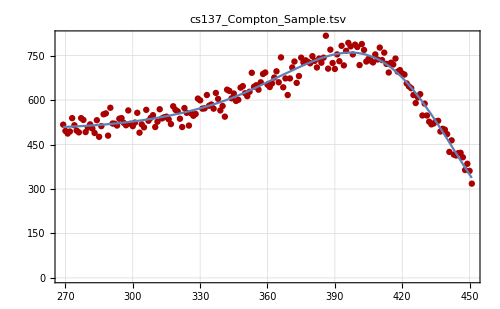
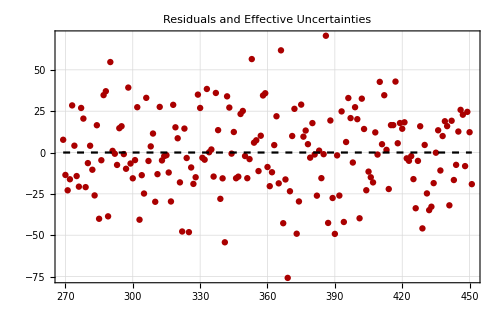
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.66 | Tedge (MeV) = 
0.475806 | 
EPE (eV/photoelectron) = 
2134.61 | sigEPE = 
6.53847 | 
Xscale (channels/MeV) = 
919.547 | sigXscale = 
0.0704417 | 
Yscale = 
(counts/channel)/(probability/MeV)
285.778 | sigYscale = 
0.517989 | 
Yoffset (counts/channel) = 
17.828 | sigYoffset = 
1.02326 | 
Xedge (channel) = 
437.526 | sigXedge = 
0.0335166 | Std. deviation = 
611.138

```mathematica
LinearDifferencePlot[]
```

```mathematica
?ComptonFit
```

ComptonFit[k_0,e_pe,x_edge] performs a CurveFit-compatible fit of a measured scintillator spectrum to a single-photon Compton scattering distribution. When calling ComptonFit[ ] k_0, e_pe, and x_edge must all be given numerical values: k_0 is the incoming photon energy (in MeV), e_pe is an initial estimate of the average energy deposited per photoelectron (in eV), and x_edge is an initial estimate of the X position of the Compton edge (channel number).

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/plastic_co60_overnight.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	60543.3
Live Time Elapsed:	60535.7
Start Time:	05/17/2018 16:02:54
Stop Time:	05/18/2018 08:51:58

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{400.8,941.8}

n= 541

302 points removed.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to remove." ]}, 
  Print[x]; 

  XRangeRemove[Sequence@@x] 
]
```

{663.2,863.}

n= 341

200 points removed.

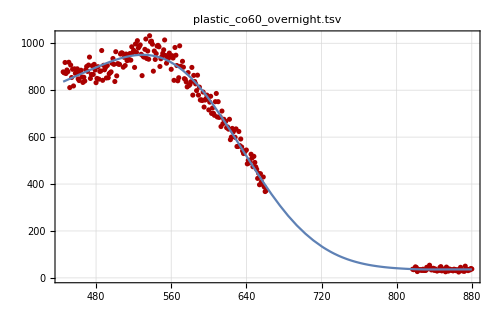
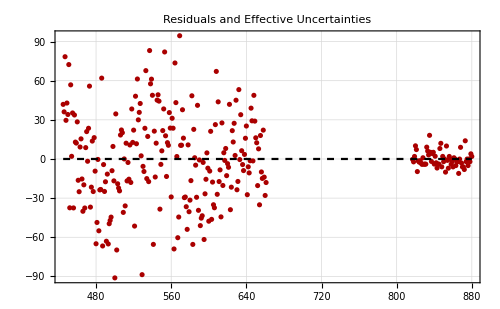
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
6001.64 | sigEPE = 
5.43436 | 
Xscale (channels/MeV) = 
1297.84 | sigXscale = 
0.045023 | 
Yscale = 
(counts/channel)/(probability/MeV)
415.893 | sigYscale = 
0.0889337 | 
Yoffset (counts/channel) = 
36.0646 | sigYoffset = 
0.125563 | 
Xedge (channel) = 
619.436 | sigXedge = 
0.0214886 | Std. deviation = 
986.973

```mathematica
LinearDifferencePlot[]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/plastic_co60_overnight.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	60543.3
Live Time Elapsed:	60535.7
Start Time:	05/17/2018 16:02:54
Stop Time:	05/18/2018 08:51:58

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

341 Y count values have had sigma values assigned.

341 X channel values have had sigma values assigned.

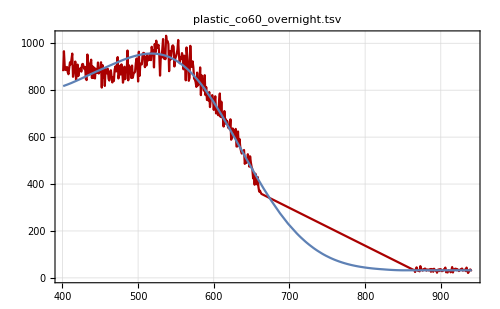
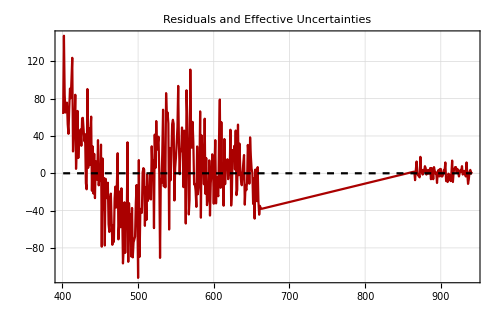
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
7509.04 | sigEPE = 
151.104 | 
Xscale (channels/MeV) = 
1293.59 | sigXscale = 
1.08858 | 
Yscale = 
(counts/channel)/(probability/MeV)
435.505 | sigYscale = 
1.39933 | 
Yoffset (counts/channel) = 
32.3698 | sigYoffset = 
0.644468 | 
Xedge (channel) = 
617.406 | sigXedge = 
0.519558 | χ^2 = 
2.00651

```mathematica
LinearDifferencePlot[]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/plastic_co60_overnight.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	60543.3
Live Time Elapsed:	60535.7
Start Time:	05/17/2018 16:02:54
Stop Time:	05/18/2018 08:51:58

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{338.8,892.6}

n= 554

470 points removed.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to remove." ]}, 
  Print[x]; 

  XRangeRemove[Sequence@@x] 
]
```

{668.2,810.4}

n= 412

142 points removed.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

381 Y count values have had sigma values assigned.

381 X channel values have had sigma values assigned.

```mathematica
ComptonFit[0.6616,2,544]
```

n = 412

y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

Fit of (x,y)  (unweighted)

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 20 iterations.

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
11593.2 | sigEPE = 
7.80046 | 
Xscale (channels/MeV) = 
1293.65 | sigXscale = 
0.0609209 | 
Yscale = 
(counts/channel)/(probability/MeV)
473.759 | sigYscale = 
0.0859853 | 
Yoffset (counts/channel) = 
22.0447 | sigYoffset = 
0.125795 | 
Xedge (channel) = 
617.434 | sigXedge = 
0.0290764 | Std. deviation = 
3019.03

Fit of (x,y±σ_y)

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
9905.15 | sigEPE = 
161.662 | 
Xscale (channels/MeV) = 
1284.86 | sigXscale = 
1.12931 | 
Yscale = 
(counts/channel)/(probability/MeV)
462.988 | sigYscale = 
1.3317 | 
Yoffset (counts/channel) = 
30.0969 | sigYoffset = 
0.801957 | 
Xedge (channel) = 
613.24 | sigXedge = 
0.538997 | χ^2 = 
3.84481

Fit of (x±σ_x,y±σ_y)

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
9905.03 | sigEPE = 
161.661 | 
Xscale (channels/MeV) = 
1284.86 | sigXscale = 
1.1293 | 
Yscale = 
(counts/channel)/(probability/MeV)
462.987 | sigYscale = 
1.3317 | 
Yoffset (counts/channel) = 
30.0972 | sigYoffset = 
0.801953 | 
Xedge (channel) = 
613.24 | sigXedge = 
0.538996 | χ^2 = 
3.84481

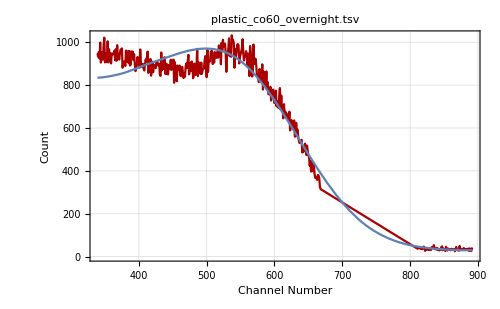
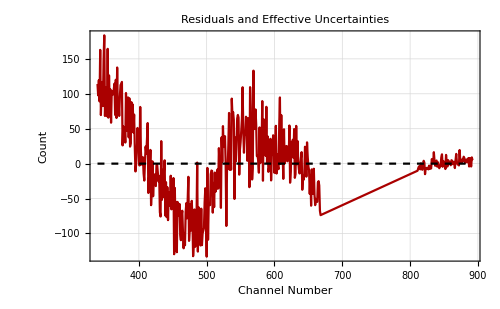
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
9905.03 | sigEPE = 
161.661 | 
Xscale (channels/MeV) = 
1284.86 | sigXscale = 
1.1293 | 
Yscale = 
(counts/channel)/(probability/MeV)
462.987 | sigYscale = 
1.3317 | 
Yoffset (counts/channel) = 
30.0972 | sigYoffset = 
0.801953 | 
Xedge (channel) = 
613.24 | sigXedge = 
0.538996 | χ^2 = 
3.84481

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

554 Y count values have had sigma values assigned.

554 X channel values have had sigma values assigned.

```mathematica
ComptonFit[0.6616,2,544]
```

n = 381

y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

Fit of (x,y)  (unweighted)

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
8681.63 | sigEPE = 
6.33287 | 
Xscale (channels/MeV) = 
1295.25 | sigXscale = 
0.0516041 | 
Yscale = 
(counts/channel)/(probability/MeV)
445.405 | sigYscale = 
0.071346 | 
Yoffset (counts/channel) = 
32.9583 | sigYoffset = 
0.0989164 | 
Xedge (channel) = 
618.2 | sigXedge = 
0.0246297 | Std. deviation = 
1758.8

Fit of (x,y±σ_y)

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
8328.19 | sigEPE = 
162.846 | 
Xscale (channels/MeV) = 
1292.4 | sigXscale = 
1.15022 | 
Yscale = 
(counts/channel)/(probability/MeV)
443.218 | sigYscale = 
1.35318 | 
Yoffset (counts/channel) = 
32.7524 | sigYoffset = 
0.566064 | 
Xedge (channel) = 
616.837 | sigXedge = 
0.548981 | χ^2 = 
2.29649

Fit of (x±σ_x,y±σ_y)

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
8327.61 | sigEPE = 
162.84 | 
Xscale (channels/MeV) = 
1292.4 | sigXscale = 
1.15018 | 
Yscale = 
(counts/channel)/(probability/MeV)
443.216 | sigYscale = 
1.35316 | 
Yoffset (counts/channel) = 
32.7521 | sigYoffset = 
0.56615 | 
Xedge (channel) = 
616.837 | sigXedge = 
0.548961 | χ^2 = 
2.29648

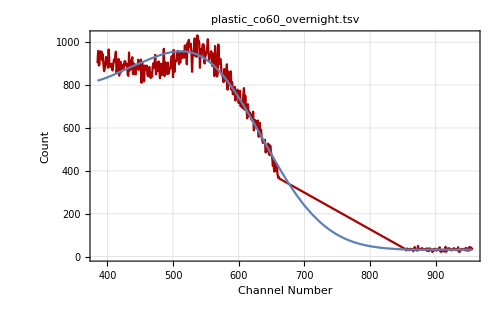
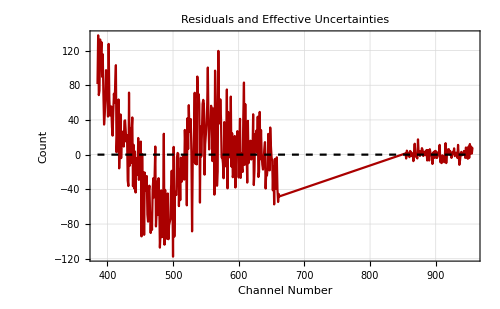
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
8327.61 | sigEPE = 
162.84 | 
Xscale (channels/MeV) = 
1292.4 | sigXscale = 
1.15018 | 
Yscale = 
(counts/channel)/(probability/MeV)
443.216 | sigYscale = 
1.35316 | 
Yoffset (counts/channel) = 
32.7521 | sigYoffset = 
0.56615 | 
Xedge (channel) = 
616.837 | sigXedge = 
0.548961 | χ^2 = 
2.29648

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/coincidence_peaks.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	4
Fine Gain:	1.762
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	326.92
Live Time Elapsed:	247
Start Time:	05/17/2018 13:58:53
Stop Time:	05/17/2018 14:04:20

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

InterpolatingFunction::dmval: Input value {0.0000162651} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

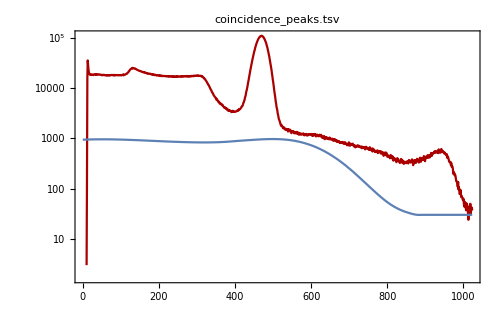
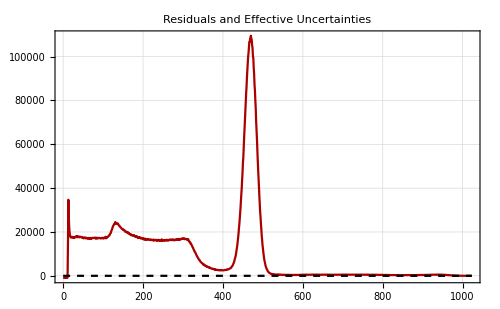
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
9905.03 | sigEPE = 
161.661 | 
Xscale (channels/MeV) = 
1284.86 | sigXscale = 
1.1293 | 
Yscale = 
(counts/channel)/(probability/MeV)
462.987 | sigYscale = 
1.3317 | 
Yoffset (counts/channel) = 
30.0972 | sigYoffset = 
0.801953 | 
Xedge (channel) = 
613.24 | sigXedge = 
0.538996 | χ^2 = 
3.84481

```mathematica
LogDifferencePlot[]
```

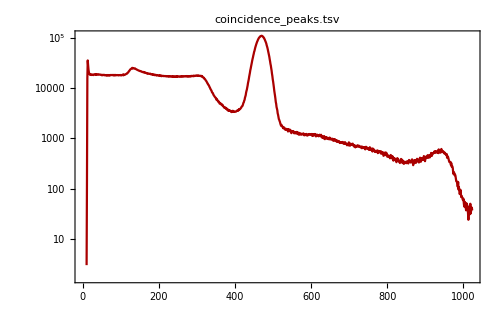

```mathematica
LogDataPlot[]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/co60_coincidence_peaks.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	650
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.546
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	635.6
Live Time Elapsed:	632.58
Start Time:	05/17/2018 14:13:11
Stop Time:	05/17/2018 14:23:47

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

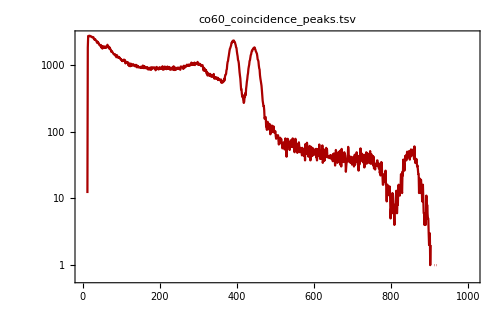

```mathematica
LogDataPlot[]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/plastic_cs137.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.696
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	484.5
Live Time Elapsed:	463.7
Start Time:	05/17/2018 15:08:19
Stop Time:	05/17/2018 15:16:24

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

InterpolatingFunction::dmval: Input value {0.0000162651} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

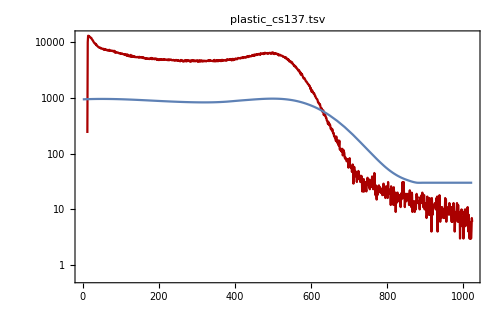
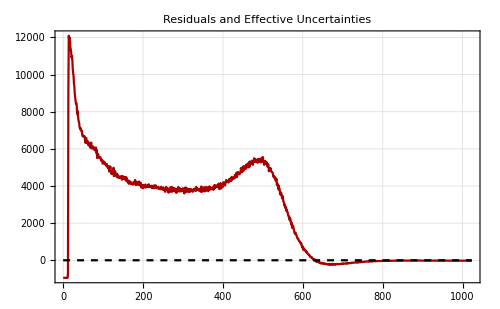
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.6616 | Tedge (MeV) = 
0.477281 | 
EPE (eV/photoelectron) = 
9905.03 | sigEPE = 
161.661 | 
Xscale (channels/MeV) = 
1284.86 | sigXscale = 
1.1293 | 
Yscale = 
(counts/channel)/(probability/MeV)
462.987 | sigYscale = 
1.3317 | 
Yoffset (counts/channel) = 
30.0972 | sigYoffset = 
0.801953 | 
Xedge (channel) = 
613.24 | sigXedge = 
0.538996 | χ^2 = 
3.84481

```mathematica
LogDifferencePlot[]
```

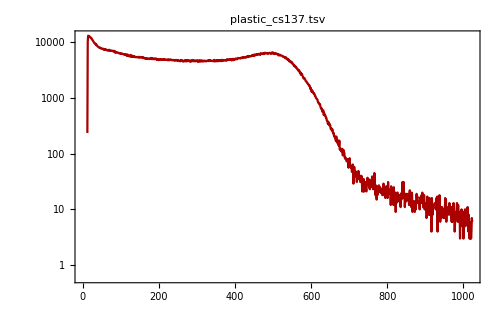

```mathematica
LogDataPlot[]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30b/30b/cs137_encore_ref.tsv

File comment header:

Spectrum Name:	Cs-137
Description:	Plastic
Student ID:
Detector Used:	Plastic Scintillator
Comments:	Step 7-Plastic
Acquisition Mode:	PHA
High Voltage:	800
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.432
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	702.26
Live Time Elapsed:	571.89
Start Time:	05/17/2018 14:45:01
Stop Time:	05/17/2018 14:56:43

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

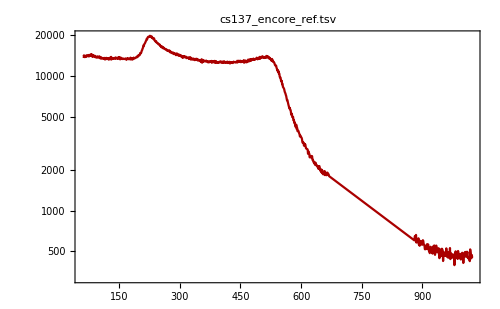

```mathematica
LogDataPlot[]
```

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LogDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to remove." ]}, 
  Print[x]; 

  XRangeRemove[Sequence@@x] 
]
```

{669.8,879.6}

n= 754

210 points removed.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/cs137_cal_plastic.mca

File comment header:

Spectrum #00015	1:48:54 PM 6/7/2018  Time: 968.44 ; MCA 1

Ch  	Count

Read 1024 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{240.6,696.2}

n= 456

104 points removed.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

563 Y count values have had sigma values assigned.

563 X channel values have had sigma values assigned.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to remove." ]}, 
  Print[x]; 

  XRangeRemove[Sequence@@x] 
]
```

{458.2,643.8}

n= 378

185 points removed.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/ba133_cal_plastic.mca

File comment header:

Spectrum #00016	1:59:16 PM 6/7/2018  Time: 474.03 ; MCA 1

Ch  	Count

Read 1024 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{80.4,383.}

n= 303

721 points removed.

```mathematica
Undo[]
```

ba133_cal_plastic.mca

n = 1024